```mathematica
array1=Import["C:\Users\Mr\Workspace\MPLAB_projects\dspic33_FFT_DSPLib.X\adc_samples.mch","Text"];
```

```mathematica
array2=StringSplit[array1]
```

{F630,1930,2E20,29A0,3220,4190,4980,49E0,4F30,5200,4F90,5E20,6930,6DC0,7230,6A30,5ED0,61F0,6990,6530,5330,33C0,0060,0640,F180,0EA0,2A50,3800,3BC0,3E50,3AB0,38D0,42B0,4BE0,4E00,60F0,7020,7020,6FA0,6B00,6800,6E90,70B0,6270,4C70,2BB0,FE50,0810,F870,0F70,31D0,3130,35D0,4200,4820,45A0,3EA0,3BA0,3B40,5330,69F0,7060,7520,7370,6B00,6BC0,7170,6F00,5E80,3F90,F7E0,EDA0,ED80,F240,2A90,33D0,3B20,4720,4830,4340,40E0,4590,44D0,4E40,5C40,6160,6A30,6F40,6BF0,7130,7900,7560,62E0,47B0,20C0,0370,F300,EE60,F130,26D0,3000,4170,4B90,4BA0,46E0,43D0,3F80,4CA0,6380,6C00,6B10,64C0,5D90,6670,74A0,77B0,6DF0,56B0,3240,0490,0280,F600,0F60,2170,2000,2ED0,3D30,4450,40E0,4460,44C0,4E10,6080,6830,6CE0,6F80,6990,67B0,6A20,6AD0,6870,5930,3B80,22F0,1550,F900,0750,18C0,25D0,3B10,4550,4080,3400,3340,39E0,4730,5E20,6C90,71D0,7040,6730,6970,73B0,7790,6F60,5740,3330,1360,1530,FEB0,0A40,1F30,22F0,3450,42B0,47E0,4450,3CE0,32A0,33A0,4D00,6240,6DC0,71F0,6D20,6EA0,74A0,7510,73B0,6700,4A50,2620,0330,EF80,EEE0,1C00,1090,3690,4740,4AC0,4460,3B30,3850,3E50,50F0,5D00,5DA0,64D0,6570,6A50,7500,7A90,7B60,6D60,4F90,3270,2400,0B90,F270,F210,F480,2800,3F30,48B0,4900,4250,3AD0,38A0,4A90,5DE0,6990,6E00,6460,5DF0,6780,7250,7A30,73D0,5C10,41D0,2D10,1000,F630,07A0,0E70,1B20,3340,39F0,3EC0,3D50,37E0,3990,4AD0,5D10,65D0,6B30}

```mathematica
(*array2={"8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","7FF0","7FF0","7FF0","7FF0","7FF0","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","7FF0","7FF0","7FF0","7FF0","7FF0","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","7FF0","7FF0","7FF0","7FF0","7FF0","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","7FF0","7FF0","7FF0","7FF0","7FF0","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","7FF0","7FF0","7FF0","7FF0","7FF0","7FF0","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","7FF0","7FF0","7FF0","7FF0","7FF0","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","7FF0","7FF0","7FF0","7FF0","7FF0","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","7FF0","7FF0","7FF0","7FF0","7FF0","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","7FF0","7FF0","7FF0","7FF0","7FF0","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","7FF0","7FF0","7FF0","7FF0","7FF0","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","7FF0","7FF0","7FF0","7FF0","7FF0","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","7FF0","7FF0","7FF0","7FF0","7FF0","7FF0","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","7FF0","7FF0","7FF0","7FF0","7FF0","8000","8000","8000","8000","8000","8000","8000"};*)
```

```mathematica
array3=FromDigits[#,16]&/@ array2;
```

```mathematica
Length[array3]

For[i=1,i<=Length[array3],i++,
If[array3[[i]]>32767,array3[[i]]=0,array3[[i]]=array3[[i]]/32767]
(*array3[[i]]=array3[[i]]/32767*)
]
```

256

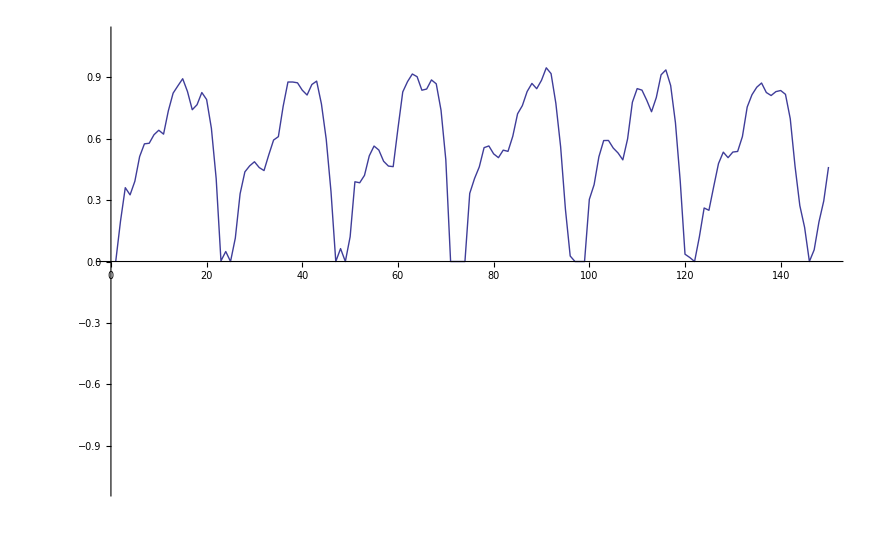

```mathematica
ListLinePlot[array3[[1;;150]],PlotRange->{-1.1,1.1}]
```

```mathematica
(*array3=Join[array3,ConstantArray[0,256]];*)
```

```mathematica
fftresults=Abs[Fourier[array3]];
```

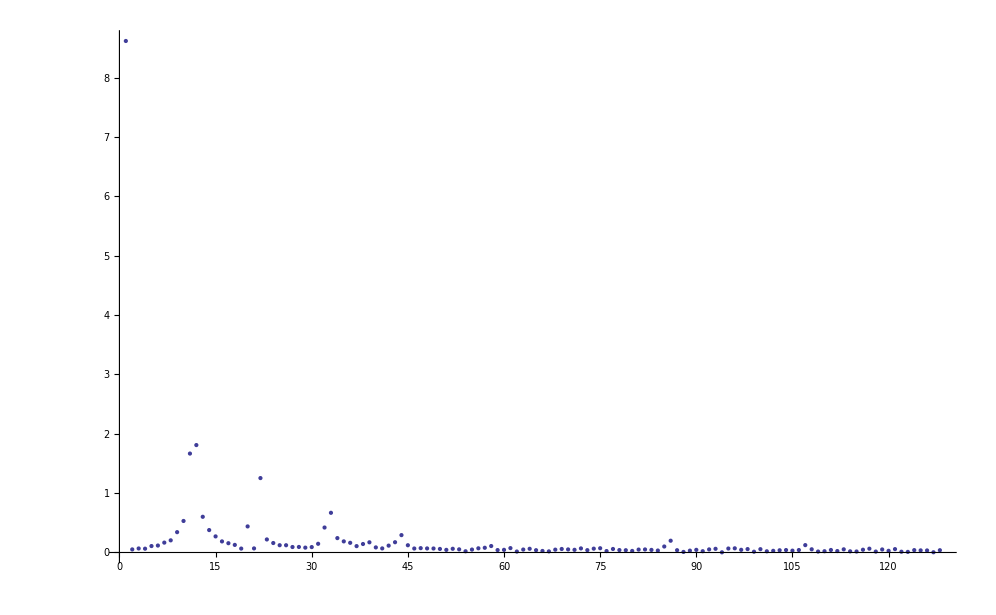

```mathematica
ListPlot[fftresults[[1;;128]],PlotRange->Full]
```